```mathematica
xeqs = (D[D[x[τ], τ], τ] == D[ϕ[x[τ], 0], x[τ]] (D[t[τ], τ]^2 - D[x[τ], τ]^2 + D[z[τ], τ]^2) )
```

x''[τ]==(2 G π ρ x[τ] (t'[τ]^2-x'[τ]^2+z'[τ]^2))/c^2

```mathematica
zeqs = (D[D[z[τ], τ], τ] == D[x[τ], τ] D[ϕ[x[τ], 0], x[τ]](2v/c D[t[τ], τ] - D[z[τ], τ]))
```

z''[τ]==(2 G π ρ x[τ] x'[τ] ((2 v t'[τ])/c-z'[τ]))/c^2

```mathematica
teqs = (D[D[t[τ], τ], τ] == 2v/c D[z[τ], τ] D[x[τ], τ] D[ϕ[x[τ], 0], x[τ]])
```

t''[τ]==(4 G π v ρ x[τ] x'[τ] z'[τ])/c^3

```mathematica
ϕ[x_, y_, τ_] := Pi * (G / c^2) * ρ * (x^2 + y^2 - R^2)
```

```mathematica
FullSimplify[{xeqs, zeqs, teqs}]
```

{x''[τ]==4.65654×10^-27 x[τ] (t'[τ]^2-1. x'[τ]^2+z'[τ]^2),z''[τ]==x[τ] x'[τ] (3.10436×10^-27 t'[τ]-4.65654×10^-27 z'[τ]),t''[τ]==3.10436×10^-27 x[τ] x'[τ] z'[τ]}

```mathematica
G = 6.67*10^(-11);
c = 3*10^8;
R = 1;
v = 1*10^8;
ρ = 1;
```

```mathematica
s = NDSolve[{xeqs, zeqs, teqs, t[0] == 0, x[0] == 0, z[0] == 0, t'[0] == 1, x'[0] == v, z'[0] == 0}, {x[τ], z[τ], t[τ]}, {τ, 0, 10}]
```

{{x[τ]→InterpolatingFunction[…][τ],z[τ]→InterpolatingFunction[…][τ],t[τ]→InterpolatingFunction[…][τ]}}

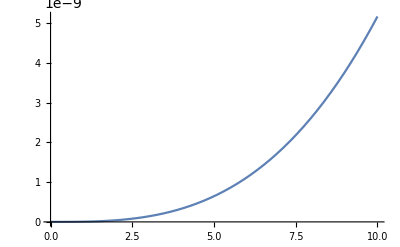

```mathematica
Plot[Evaluate[z[τ]/.s],{τ,0,10},PlotRange->All]
```

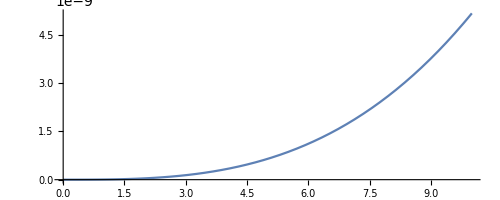

```mathematica
ParametricPlot[Evaluate[{t[τ],z[τ]}/.s],{τ,0,10}]
```